```mathematica
Competing cells(self renewal regulated) 
Differentiations = 1
```

cells Competing regulated renewal self

1

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t]}}

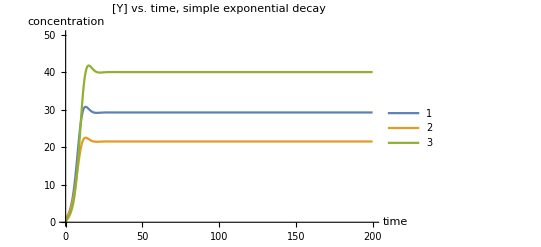

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+Z[t]))-1)(1.1*k)*X [t],
Y'[t] == (2*(P*kd/(kd+Z[t]))-1)k *Y[t],
Z'[t] == (1-(P*kd/(kd+Z[t])))*k*(2*X[t]+Y[t]) - d*Z[t],

X[0]==Yzero, Y[0]==Yzero, Z[0]==0
};
parameters1 = {k->1,Yzero-> 1, P ->0.70, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t]},{t,0,200}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,200},PlotStyle->Thick,PlotRange->{0, 50},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay",
PlotLegends -> Automatic]
```

```mathematica
Competing cells(self renewal regulated) 
Differentiations = 1
Perturbed from steady state
```

cells Competing regulated renewal self

1

from Perturbed state steady

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t]}}

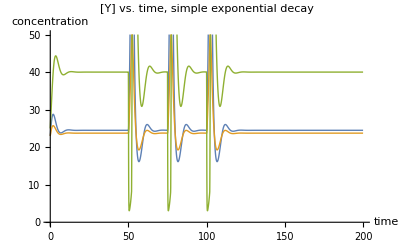

{24.4956}

{24.4956}

```mathematica
ClearAll["Global`*"]
pulseStart = 50; pulseStop = 52;
pulse[time_,pulseAmplitude_]:=Piecewise[{{0, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0,time>pulseStop}}]
(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+Z[t]))-1)(2*k)*X [t],
Y'[t] == (2*(P*kd/(kd+Z[t]))-1)k *Y[t],
Z'[t] == (1-(P*kd/(kd+Z[t])))*k*(2*X[t]+Y[t]) - (d+pulse[t,10]+pulse[t-25,10]+pulse[t-50,10])*Z[t],

X[0]==Yzero, Y[0]==Yzero, Z[0]==25
};
parameters1 = {k->1.1,Yzero-> 23, P ->0.70, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t]},{t,0,200}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,200},PlotStyle->Thick,PlotRange->{0, 50},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
X[t]/.solution1/.t-> 40.0
X[t]/.solution1/.t-> 150.0
```

```mathematica
Competing cells(self renewal regulated) 
Differentiations = 2
```

cells Competing regulated renewal self

2

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t],T[t]→InterpolatingFunction[…][t]}}

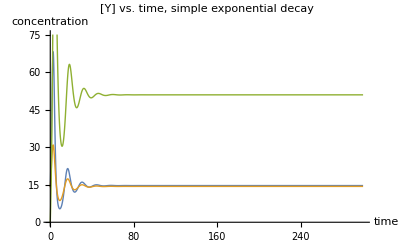

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+T[t]))-1)(2*k)*X [t],
Y'[t] == (2*(P*kd/(kd+T[t]))-1)k *Y[t],
Z'[t] == (1-(P*kd/(kd+T[t])))*((2*k)*X[t]+k*Y[t]) + (2*((P-0.3)*kd/(kd+T[t]))-1)*k*Z[t],
T'[t]==(1- ((P-0.3)*kd/(kd+T[t])))*k*Z[t]-d*T[t],
X[0]==Yzero, Y[0]==Yzero, Z[0]==0, T[0]==0
};
parameters1 = {k->1.1,Yzero-> 14, P ->0.7, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t],T[t]},{t,0,300}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,300},PlotStyle->Thick,PlotRange->{0,75},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

```mathematica
Competing cells(self renewal regulated) 
Differentiations = 2
Perturbed from steady state
```

cells Competing regulated renewal self

2

from Perturbed state steady

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t],T[t]→InterpolatingFunction[…][t]}}

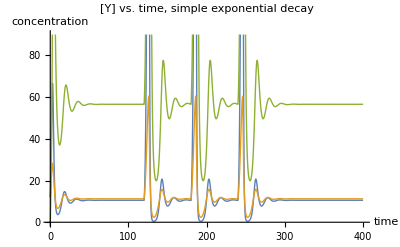

```mathematica
ClearAll["Global`*"]
pulseStart = 120; pulseStop = 126;
pulse[time_,pulseAmplitude_]:=Piecewise[{{0, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0,time>pulseStop}}]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+T[t]))-1)(2*k)*X [t],
Y'[t] == (2*(P*kd/(kd+T[t]))-1)k *Y[t],
Z'[t] == (1-(P*kd/(kd+T[t])))*((2*k)*X[t]+k*Y[t]) + (2*((P-0.2)*kd/(kd+T[t]))-1)*k*Z[t],
T'[t]==(1- ((P-0.2)*kd/(kd+T[t])))*k*Z[t]-(d+pulse[t,10]+pulse[t-60,10]+pulse[t-120,10])*T[t],
X[0]==Yzero, Y[0]==Yzero, Z[0]==0, T[0]==0
};
parameters1 = {k->1.1,Yzero-> 12, P ->0.7, d->1, kd ->100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t],T[t]},{t,0,400}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,400},PlotStyle->Thick,PlotRange->{0,90},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

```mathematica
X[t]/.solution1/.t-> 50.0
X[t]/.solution1/.t-> 400.0
```

{11.3164}

{11.3058}

```mathematica
{11.305807548521512}
```

```mathematica
Competing cells division independant of division 
(Self renewal and regeneration limited) 
Differentiations = 1
```

cells Competing division^2 independant of

and limited regeneration renewal Self

1

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t]}}

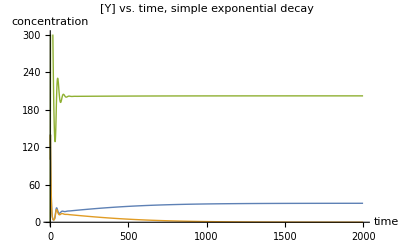

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == 1.01*(k*kd/(kd+Z[t]))*X [t] - (P*Z[t]/(kd+Z[t]))*X[t],
Y'[t] == (k*kd/(kd+Z[t])) *Y[t] - (P*Z[t]/(kd+Z[t]))*Y[t],
Z'[t] == (1-(P*Z[t]/(kd+Z[t])))*(X[t]+Y[t]) - d*Z[t],

X[0]==Yzero, Y[0]==Yzero, Z[0]==0
};
parameters1 = {k->1,Yzero-> 100, P ->0.5, d->0.1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t]},{t,0,2000}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,2000},PlotStyle->Thick,PlotRange->{0, 300},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

```mathematica
Competing cells division independant of division 
(Self renewal and regeneration limited) 
Differentiations = 2
```

cells Competing division^2 independant of

and limited regeneration renewal Self

2

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t],T[t]→InterpolatingFunction[…][t]}}

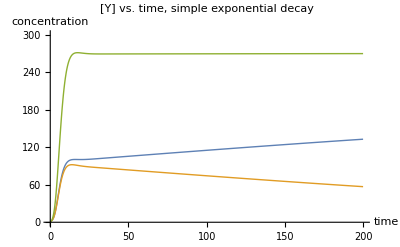

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == 1.01*(k*kd/(kd+T[t]))*X [t] - (P*T[t]/(kd+T[t]))*X[t],
Y'[t] == (k*kd/(kd+T[t])) *Y[t] - (P*T[t]/(kd+T[t]))*Y[t],
Z'[t] == (1-(P*T[t]/(kd+T[t])))*(X[t]+Y[t]) - (P*T[t]/(kd+T[t]))*Z[t],
T[t]== (1-(P*T[t]/(kd+T[t])))*Z[t] -d*T[t],

X[0]==Yzero, Y[0]==Yzero, Z[0]==0, T[0]==0
};
parameters1 = {k->1,Yzero-> 1, P ->0.70, d->0.1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t], T[t]},{t,0,200}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,200},PlotStyle->Thick,PlotRange->{0, 300},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

```mathematica
Competing cells Differentiation coupled to division 
(Self renewal and regeneration limited) 
Differentiations = 2
```

cells Competing coupled Differentiation division to

and limited regeneration renewal Self

2

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t],T[t]→InterpolatingFunction[…][t]}}

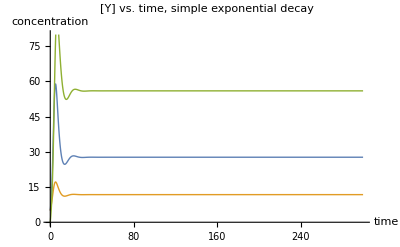

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+T[t]))-1)(2*(k*kd/(kd+T[t])))*X [t],
Y'[t] == (2*(P*kd/(kd+T[t]))-1)*(k*kd/(kd+T[t]))*Y[t],
Z'[t] == (1-(P*kd/(kd+T[t])))*(k*kd/(kd+T[t]))(2*X[t]+Y[t]) + (2*((P-0.3)*kd/(kd+T[t]))-1)*k*Z[t],
T'[t]==(1- ((P-0.3)*kd/(kd+T[t])))*k*Z[t]-d*T[t],
X[0]==Yzero, Y[0]==Yzero, Z[0]==0, T[0]==0
};
parameters1 = {k->1,Yzero-> 5, P ->0.7, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t],T[t]},{t,0,300}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,300},PlotStyle->Thick,PlotRange->{0,80},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

```mathematica
Competing cells Differentiation coupled to division 
(Self renewal and regeneration limited) 
Differentiations = 2
Perturbed from steady state
```

cells Competing coupled Differentiation division to

and limited regeneration renewal Self

2

from Perturbed state steady

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t],T[t]→InterpolatingFunction[…][t]}}

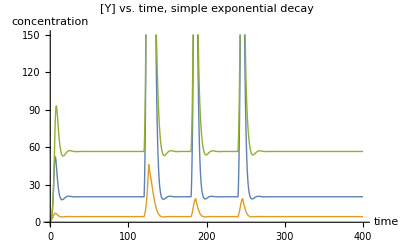

```mathematica
ClearAll["Global`*"]
pulseStart = 120; pulseStop = 126;
pulse[time_,pulseAmplitude_]:=Piecewise[{{0, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0,time>pulseStop}}]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+T[t]))-1)(2*(k*kd/(kd+T[t])))*X [t],
Y'[t] == (2*(P*kd/(kd+T[t]))-1)(k*kd/(kd+T[t])) *Y[t],
Z'[t] == (1-(P*kd/(kd+T[t])))(k*kd/(kd+T[t]))(2*X[t]+Y[t]) + (2*((P-0.2)*kd/(kd+T[t]))-1)*k*Z[t],
T'[t]==(1- ((P-0.2)*kd/(kd+T[t])))*k*Z[t]-(d+pulse[t,100]+pulse[t-60,10]+pulse[t-120,10])*T[t],
X[0]==Yzero, Y[0]==Yzero, Z[0]==0, T[0]==0
};
parameters1 = {k->1.1,Yzero-> 1, P ->0.7, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t],T[t]},{t,0,400}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,400},PlotStyle->Thick,PlotRange->{0,150},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

# Differentiation uncoupled to division is a dominant phenotype with respect to steady state levels of 2 stem cell populations with unique proliferation rates.

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t]}}

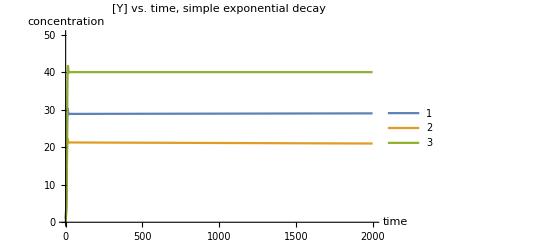

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+Z[t]))-1)(1.1*k)*X [t] - 0.01*X[t],
Y'[t] == (2*(P*kd/(kd+Z[t]))-1)k *Y[t] -0.01*Y[t],
Z'[t] == (1-(P*kd/(kd+Z[t])))*k*(2*X[t]+Y[t]) + 0.01*(X[t]+Y[t])- d*Z[t],

X[0]==Yzero, Y[0]==Yzero, Z[0]==0
};
parameters1 = {k->1,Yzero-> 1, P ->0.70, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t]},{t,0,2000}]
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,2000},PlotStyle->Thick,PlotRange->{0, 50},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay",
PlotLegends -> Automatic]
```

## Analytical Analyses

```mathematica
dxdt = X'[t]== (2*P*kd/(dk+Z[t])-1)*Vx*X[t];
dydt = Y'[t] == (2*P*kd/(dk+Z[t])-1)*Vy*Y[t];
dzdt = Z'[t]  == (1-P*kd/(dk+Z[t]))*(Vx*X[t]+Vy*Y[t]) - d*Z[t];

dxdtss = Vx X (-1+(2 kd P)/(kd+Z));
dydtss=Vy Y (-1+(2 kd P)/(kd+Z));
dzdtss=-d Z+(Vx X+Vy Y) (1-(kd P)/(kd+Z));
zss = Solve[dxdtss ==0,Z]//Flatten
yss = Solve[dzdtss==0,Y]//Flatten
```

{Z→kd (-1+2 P)}

{Y→(kd Vx X-kd P Vx X-d kd Z+Vx X Z-d Z^2)/(Vy (-kd+kd P-Z))}

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x});
a={dxdtss,dydtss,dzdtss};
b={X,Y,Z};
jacobian  = JacobianMatrix[a,b]/.{X-> X,Y-> (kd Vx X-kd P Vx X-d kd Z+Vx X Z-d Z^2)/(Vy (-kd+kd P-Z)),Z->kd (-1+2 P)};
eig = Eigenvalues[jacobian];
eig[[2]]//Simplify
```

-1/(8 kd P (kd (-1+P)-Z))(-4 d kd^2 P+4 d kd^2 P^2+d kd Z-4 d kd P Z+d Z^2+√(d^2 (4 kd^2 (-1+P) P+Z^2+kd (Z-4 P Z))^2-16 kd P (kd (-1+P)-Z) (kd ((-1+P) Vx^2 X-(-1+P) Vx Vy X-d Vy Z)-Z (Vx^2 X-Vx Vy X+d Vy Z))))

```mathematica
Manipulate[eig[[2]]/.{Z->kd (-1+2 P),Y->(kd Vx X-kd P Vx X-d kd Z+Vx X Z-d Z^2)/(Vy (-kd+kd P-Z))}/.{X->x,Vx->1.1,Vy->2.2,P ->0.70, d->1, kd -> 100},{x,0,1000,Appearance->"Labeled"}]//Simplify
```

```mathematica
pulseStart = 50; pulseStop = 52;
pulse[time_,pulseAmplitude_]:=Piecewise[{{0, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0,time>pulseStop}}]
(* defining system and giving numerical values to parameters *)
system1 = {
X'[t] == (2*(P*kd/(kd+Z[t]))-1)(2*k)*X [t],
Y'[t] == (2*(P*kd/(kd+Z[t]))-1)k *Y[t],
Z'[t] == (1-(P*kd/(kd+Z[t])))*k*(2*X[t]+Y[t]) - (d+pulse[t,10]+pulse[t-25,10]+pulse[t-50,10])*Z[t],

X[0]==Yzero, Y[0]==Yzero, Z[0]==25
};
parameters1 = {k->1.1,Yzero-> 23, P ->0.70, d->1, kd -> 100};
case1 = system1/.parameters1;
solution1 = NDSolve[case1,{X[t],Y[t],Z[t]},{t,0,200}];
Plot[{X[t]/.solution1,Y[t]/.solution1,Z[t]/.solution1 },{t,0,200},PlotStyle->Thick,PlotRange->{0, 50},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
X[t]/.solution1/.t-> 40.0;
X[t]/.solution1/.t-> 150.0;
```

-Graphics-